

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
Manipulate[
Plot[a x^3,{x,-5,5}]
,{a,-5,5}]
```

```mathematica
Manipulate[
Plot[a x^3,{x,-5,5},PlotRange->{-2,2}]
,{a,-5,5}]
```

```mathematica
x^3-x^2
```

-x^2+x^3

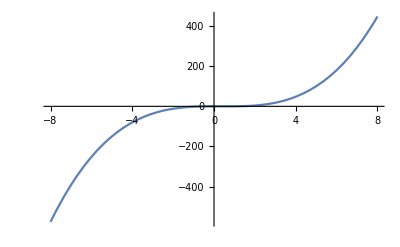

```mathematica
Plot[-x^2+x^3,{x,-8,8}]
```

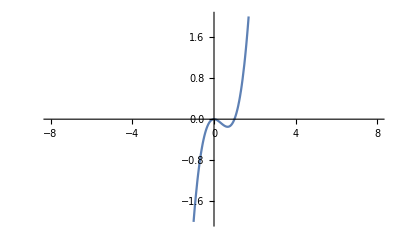

```mathematica
Plot[-x^2+x^3,{x,-8,8},PlotRange->{-2,2}]
```

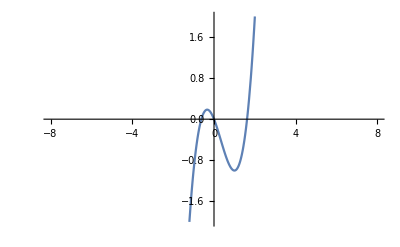

```mathematica
Plot[-x^2+x^3-x,{x,-8,8},PlotRange->{-2,2}]
```

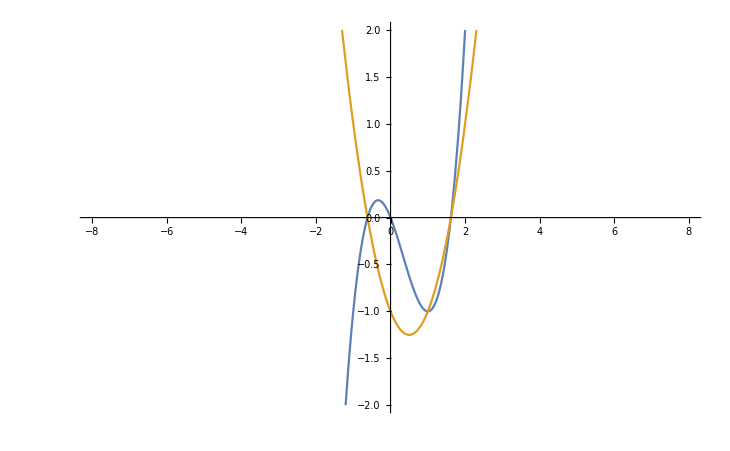

```mathematica
Plot[{-x^2+x^3-x,-x+x^2-1},{x,-8,8},PlotRange->{-2,2}]
```

```mathematica
Table[(x^3-x^2-1)/x^a,{a,0,10}]
```

{-1-x^2+x^3,(-1-x^2+x^3)/x,(-1-x^2+x^3)/x^2,(-1-x^2+x^3)/x^3,(-1-x^2+x^3)/x^4,(-1-x^2+x^3)/x^5,(-1-x^2+x^3)/x^6,(-1-x^2+x^3)/x^7,(-1-x^2+x^3)/x^8,(-1-x^2+x^3)/x^9,(-1-x^2+x^3)/x^10}

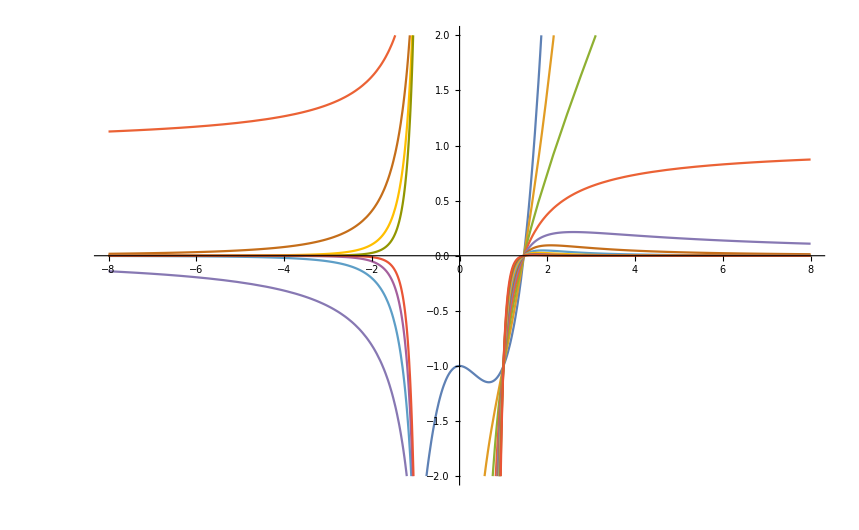

```mathematica
Plot[
{-1-x^2+x^3,(-1-x^2+x^3)/x,(-1-x^2+x^3)/x^2,(-1-x^2+x^3)/x^3,(-1-x^2+x^3)/x^4,(-1-x^2+x^3)/x^5,(-1-x^2+x^3)/x^6,(-1-x^2+x^3)/x^7,(-1-x^2+x^3)/x^8,(-1-x^2+x^3)/x^9,(-1-x^2+x^3)/x^10}
,{x,-8,8},PlotRange->{-2,2}]
```

```mathematica
Manipulate[
Plot[(x^3-x^2-1)/x^a,{x,-3,3},PlotRange->{-2,2}]
,{a,0,20}]
```

```mathematica
Manipulate[
Plot[(x^3-x^2-1)/x^a,{x,-3,3},PlotRange->{{-2,2},{-2,2}}]
,{a,0,20}]
```

```mathematica
Manipulate[
Plot[(x^3-x)/x^a,{x,-3,3},PlotRange->{{-2,2},{-2,2}}]
,{a,0,20}]
```

```mathematica
Manipulate[
Plot[(x^3-x)/x^a,{x,-3,3},PlotRange->{{-2,2},{-2,2}}]
,{a,0,30,1}]
```

```mathematica
Manipulate[
Plot[Abs[(x^3-x)/x^a],{x,-3,3},PlotRange->{{-2,2},{-2,2}}]
,{a,0,30,1}]
```

```mathematica
ArcCurvature[{x,(x^3-x)/x^30},x]
```

6 Abs[x]^28 √(1/((841-1566 x^2+729 x^4+x^60)^3)(17682025 Abs[x]^2-65850300 x^2 Abs[x]^2+91963350 x^4 Abs[x]^2-57080700 x^6 Abs[x]^2+13286025 x^8 Abs[x]^2+63075 x^60 Abs[x]^2-114840 x^62 Abs[x]^2+52326 x^64 Abs[x]^2+25 x^120 Abs[x]^2-35364050 x Abs[x] Abs'[x]+131700600 x^3 Abs[x] Abs'[x]-183926700 x^5 Abs[x] Abs'[x]+114161400 x^7 Abs[x] Abs'[x]-26572050 x^9 Abs[x] Abs'[x]-84100 x^61 Abs[x] Abs'[x]+156600 x^63 Abs[x] Abs'[x]-72900 x^65 Abs[x] Abs'[x]-50 x^121 Abs[x] Abs'[x]+17682025 x^2 Abs'[x]^2-65850300 x^4 Abs'[x]^2+91963350 x^6 Abs'[x]^2-57080700 x^8 Abs'[x]^2+13286025 x^10 Abs'[x]^2+42050 x^62 Abs'[x]^2-78300 x^64 Abs'[x]^2+36450 x^66 Abs'[x]^2+25 x^122 Abs'[x]^2))

```mathematica
FullSimplify[ArcCurvature[{x,(x^3-x)/x^30},x],x∈Reals]
```

Piecewise[{{-6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2], x≤0}, {6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2], True}}]

```mathematica
PiecewiseExpand[Piecewise[{{-6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2],x≤0}},6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2]]]
```

Piecewise[{{-6 x^59 (-145+126 x^2) √(1/((841-1566 x^2+729 x^4+x^60)^3)), 0<x≤(√(145/14))/3||x<-(√(145/14))/3}, {6 x^59 (-145+126 x^2) √(1/((841-1566 x^2+729 x^4+x^60)^3)), True}}]

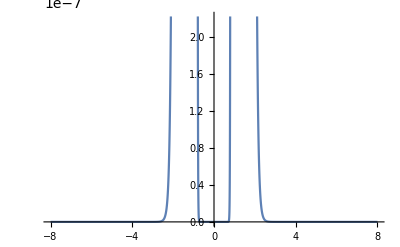

```mathematica
Plot[Piecewise[{{-6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2],x≤0}},6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2]],{x,-8,8}]
```

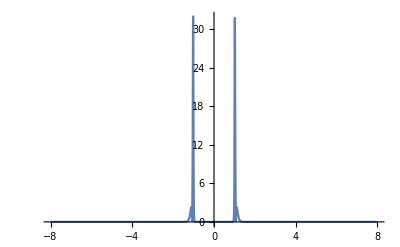

```mathematica
Plot[Piecewise[{{-6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2],x≤0}},6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2]],{x,-8,8},PlotRange->Full]
```

```mathematica
Manipulate[
NIntegrate[Piecewise[{{-6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2], x≤0}, {6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2], True}}],{x,-a,a}]
,{a,0,100}]
```

```mathematica
Limit[
NIntegrate[Piecewise[{{-6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2], x≤0}, {6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2], True}}],{x,-a,a}]
,a->∞]
```

NIntegrate::nlim: x = -1. a is not a valid limit of integration.

lim_(a→∞) NIntegrate[Piecewise[{{-6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2], x≤0}, {6 x^59 √(1/((841-1566 x^2+729 x^4+x^60)^3)) Abs[145-126 x^2], True}}],{x,-a,a}]

```mathematica
Table[(x^3-x)x^a,{a,0,10}]
```

{-x+x^3,x (-x+x^3),x^2 (-x+x^3),x^3 (-x+x^3),x^4 (-x+x^3),x^5 (-x+x^3),x^6 (-x+x^3),x^7 (-x+x^3),x^8 (-x+x^3),x^9 (-x+x^3),x^10 (-x+x^3)}

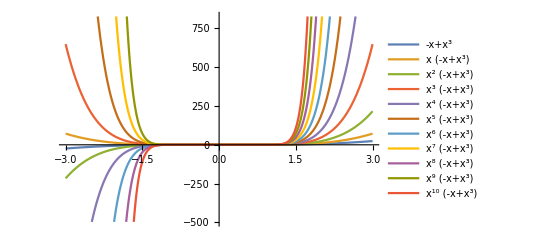

```mathematica
Plot[
{-x+x^3,x (-x+x^3),x^2 (-x+x^3),x^3 (-x+x^3),x^4 (-x+x^3),x^5 (-x+x^3),x^6 (-x+x^3),x^7 (-x+x^3),x^8 (-x+x^3),x^9 (-x+x^3),x^10 (-x+x^3)}
,{x,-3,3},PlotLegends->"Expressions"]
```

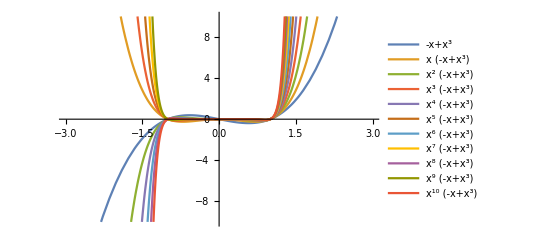

```mathematica
Plot[
{-x+x^3,x (-x+x^3),x^2 (-x+x^3),x^3 (-x+x^3),x^4 (-x+x^3),x^5 (-x+x^3),x^6 (-x+x^3),x^7 (-x+x^3),x^8 (-x+x^3),x^9 (-x+x^3),x^10 (-x+x^3)}
,{x,-3,3},PlotLegends->"Expressions",PlotRange->{-10,10}]
```

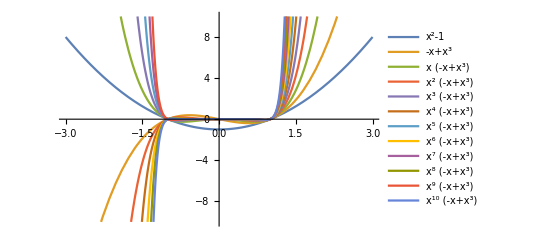

```mathematica
Plot[
{x^2-1,-x+x^3,x (-x+x^3),x^2 (-x+x^3),x^3 (-x+x^3),x^4 (-x+x^3),x^5 (-x+x^3),x^6 (-x+x^3),x^7 (-x+x^3),x^8 (-x+x^3),x^9 (-x+x^3),x^10 (-x+x^3)}
,{x,-3,3},PlotLegends->"Expressions",PlotRange->{-10,10}]
```

```mathematica
ReImPlot[z^2,{-5-5I,5+5I}]
```

ReImPlot::pllim: Range specification {-5-5 ⅈ,5+5 ⅈ} is not of the form {x, xmin, xmax}.

ReImPlot[z^2,{-5-5 ⅈ,5+5 ⅈ}]

```mathematica
ReImPlot[z^2,{-5,5}]
```

ReImPlot::pllim: Range specification {-5,5} is not of the form {x, xmin, xmax}.

ReImPlot[z^2,{-5,5}]

```mathematica
ReImPlot[z^2,{z,-5-5I,5+5I}]
```

ReImPlot::plln: Limiting value -5-5 ⅈ in {z,-5-5 ⅈ,5+5 ⅈ} is not a machine-sized real number.

ReImPlot[z^2,{z,-5-5 ⅈ,5+5 ⅈ}]

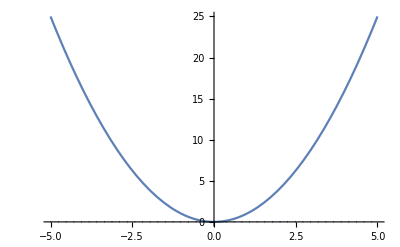

```mathematica
ReImPlot[z^2,{z,-5,5}]
```

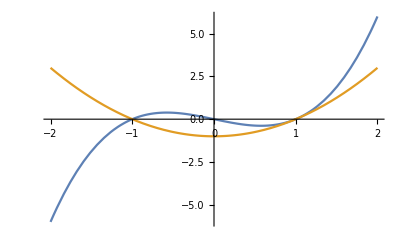

```mathematica
Plot[{x^3-x,x^2-1},{x,-2,2}]
```